```mathematica
NotebookDirectory[]
```

/Users/jogh/Dropbox/SIDIS (1)/paper/code/

# Definitions

general definitions

```mathematica
SetDirectory[NotebookDirectory[]]

(*dot product definition*)
Mdot[a_,b_]:=
(a//Simplify//Part[#,1]&)(b//Simplify//Part[#,2]&)+
(a//Simplify//Part[#,2]&)(b//Simplify//Part[#,1]&)-
(a//Simplify//Part[#,3]&).(b//Simplify//Part[#,3]&)//
ReplaceAll[#,Dot[x_,ZeroT]->0]&//
ReplaceAll[#,ZeroT->0]&//
ReplaceRepeated[#,{Dot[x_+y_,z_]|Dot[z_,x_+y_]->Dot[x,z]+Dot[y,z]}]&//
ReplaceRepeated[#,{Dot[Times[-1,x_],Times[-1,y_]]->Dot[x,y]}]&//
ReplaceRepeated[#,{Dot[Times[-1,x_],y_]|Dot[x_,Times[-1,y_]]->-Dot[x,y]}]&//ReplaceRepeated[#,{Dot[c_ qT,y_]|Dot[y_,c_ qT]->c Dot[qT,y]}]&//ReplaceAll[#,Dot[x_,x_]->x^2]&//ReplaceAll[#,Dot[0,x_]|Dot[x_,0]->0]&

Mdot0[a_,b_]:=
(a//Simplify//Part[#,1]&)(b//Simplify//Part[#,2]&)+
(a//Simplify//Part[#,2]&)(b//Simplify//Part[#,1]&)-
(a//Simplify//Part[#,3]&).(b//Simplify//Part[#,3]&)//
ReplaceAll[#,Dot[x_,ZeroT]->0]&//
ReplaceAll[#,ZeroT->0]&

assumptions={M>0,Q>0,MB>0,Δk>0,0<ξ<1,0<ζ<1,0<xbj<1,0<zh<1,PT>0,qT>0,yh∈Reals,zN>0,xN>0,ykf∈Reals,yki∈Reals,yh∈Reals,δkT>0,kf>0,ki>0,η>0,ykf0∈Reals,yp∈Reals,ⅇ^(2 yh) Q^2>qT^2};
$Assumptions=assumptions

getfunction[symbol_]:=Module[
{variables,argspassed},
argspassed=symbol//Definition//InputForm//ToString//StringMatchQ[#,__~~"_"~~__]&;

If[argspassed,
variables=symbol//Definition//InputForm//ToString//StringCases[#,__~~"_"]&//StringDelete[#,{__~~"[","_"}]&//StringSplit[#,","]&//Flatten;
variables=ToExpression/@variables;
(symbol@@variables),
symbol
]
]
```

/Users/jogh/Dropbox/SIDIS (1)/paper/code

{M>0,Q>0,MB>0,Δk>0,0<ξ<1,0<ζ<1,0<xbj<1,0<zh<1,PT>0,qT>0,yh∈ℝ,zN>0,xN>0,ykf∈ℝ,yki∈ℝ,yh∈ℝ,δkT>0,kf>0,ki>0,η>0,ykf0∈ℝ,yp∈ℝ,ⅇ^(2 yh) Q^2>qT^2}

Four momenta

```mathematica
(*In the Breit Frame, light-cone coordinates*)
qbreit={-Q/(√2),Q/(√2),ZeroT};
Pbreit={Q/(xN √2),(xN M^2)/(√2 Q),ZeroT};
PBbreit={(MB^2+zN^2 qT^2)/(√2 zN Q),(zN Q)/(√2),-zN qT};
PBbreit2={(MB^2+PT^2)/(√2 zN Q),(zN Q)/(√2), PT};

kibreit={Q/(xNhat √2),(xNhat (ki^2+kiTbreit^2))/(√2 Q),kiTbreit};
kfbreit={(kf^2+(-zNhat qT +δkT).(-zNhat qT +δkT))/(√2 zNhat Q),(zNhat Q)/(√2),-zNhat qT +δkT};

kbreit=kfbreit-qbreit;

kXbreit=kibreit+qbreit-kfbreit;

kXbreit2=kibreit+qbreit-kfbreit
```

{-Q/(√2)+Q/(√2 xNhat)-(kf^2+(-qT zNhat+δkT).(-qT zNhat+δkT))/(√2 Q zNhat),Q/(√2)+((ki^2+kiTbreit^2) xNhat)/(√2 Q)-(Q zNhat)/(√2),kiTbreit+ZeroT+qT zNhat-δkT}

```mathematica
Clear[ltemp,lptemp,lminussol,ltsol,lplussol];
ltemp={lplus,lminus,lt};
lptemp=ltemp-qbreit/.ZeroT->0;
lminussol=Mdot[lptemp,lptemp]==Mdot[ltemp,ltemp]//Simplify//Solve[#,lminus]&//Flatten;
ltsol=(ltemp/.lminussol//Mdot[#,#]&)==0//Solve[#,lt]&//Part[#,2]&;
lplussol=(Mdot[qbreit,Pbreit]/Mdot[ltemp,Pbreit]/.lminussol//Apart)==y//Solve[#,lplus]&//Simplify//Flatten;
lbreit=ltemp/.lminussol/.lplussol/.xN->XN[xbj,M,Q]//Apart//Simplify//ReplaceAll[#,M->Q  γ /2/xbj]&//FullSimplify;
```

```mathematica
Clear[l]
```

```mathematica
trentodot=l.Ph -1/(P.q) (1+γ^2) (l.q  Ph.P+l.P  Ph.q)+γ^2/(1+γ^2)((q.l q.Ph)/Q^2+(P.l P.Ph)/M^2)/.Dot->Mdot;
trentodot2=trentodot/.{Ph->PBbreit2,l->lbreit,P->Pbreit,q->qbreit}/.ZeroT.ZeroT->0/.Dot[x_,ZeroT]|Dot[ZeroT,x_]->0//ReplaceAll[#,{zN->zh,xN->XN[xbj,Q  γ /2/xbj,Q],M->Q  γ /2/xbj,MB->0}]&//Apart//Simplify;
```

Part::partd: Part specification l⟦1⟧ is longer than depth of object.

Part::partd: Part specification Ph⟦2⟧ is longer than depth of object.

Part::partd: Part specification l⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

LC momentum fractions

```mathematica
Clear[XN,ZN,Xh]

XN[xbj_,M_,Q_]=2 xbj/(1+√(1+(4 xbj^2 M^2)/Q^2));
ZN[zh_,xN_,qT_,MB_,M_,Q_]=Mdot[PBbreit,Pbreit]/Mdot[Pbreit,qbreit]==zh//Solve[#,zN]&//FullSimplify//Part[#,2,1,2]&;
ZN2[zh_,xbj_,PT_,MB_,M_,Q_]=Mdot[PBbreit2,Pbreit]*2 xbj /Q^2==zh//Solve[#,zN]&//FullSimplify//Part[#,2,1,2]&//ReplaceAll[#,xN->XN[xbj,M,Q]]&//FullSimplify[#,Assumptions->assumptions]&;

Xh[xbj_,zN_,qT_,MB_,Q_]=Mdot[qbreit,PBbreit]*2* xbj/Q^2//Simplify;
```

Ratios R1, R2, R3 neglecting angular dependence

## main definitions

```mathematica
(*collinearity*)
(*R1=Mdot[PBbreit,kfbreit]/Mdot[PBbreit,kibreit]//Expand//ReplaceAll[#,qT.kiTbreit->-qT kiTbreit]&//Simplify;(*original*)*)
R1=Mdot[PBbreit,kfbreit]/Mdot[PBbreit,kibreit]//Expand//ReplaceAll[#,Dot->Times]&//Simplify;
(*transverse hardness ratio notice squared and sqrt root is necessary, since Abs computes norm for a complex number *)
R2=Mdot[kbreit,kbreit]/Q^2//FullSimplify//ReplaceAll[#,qT.δkT->qT δkT]&;
R2=Sqrt[R2^2];
(*parton configuration ratio*)
R3=Mdot[kXbreit,kXbreit]/Q^2//ReplaceAll[#,{Dot->Times}]&//Power[#,2]&//Sqrt;
R3test=Mdot[kXbreit,kXbreit]/Q^2/.zNhat->zh/ζ//ReplaceAll[#,{Dot->Times}]&//Simplify//Power[#,2]&//Sqrt;
R3test2=Mdot[kXbreit,kXbreit]/Q^2//ReplaceAll[#,{Dot->Times}]&//Simplify;


(*missing mass for hadronic process ratio*)
replacekin1
```

{zh→0.25,ξ→0.2,ζ→0.3}

```mathematica
testR3[xbj_,ξ_,qT_]=R3//.replacefunctions/.kiTbreit|δkT|ki|kf->Δk/.Δk->0.3/.Q->2/.zh->0.25/.ζ->0.3/.MB->0.14;
testR3v2[xbj_,r_,qT_]=R3//.replacefunctions/.kiTbreit|δkT|ki|kf->Δk/.Δk->0.3/.Q->2/.zh->0.25/.ζ->0.3/.MB->0.14/.ξ->(1-xbj)r + xbj ;
```

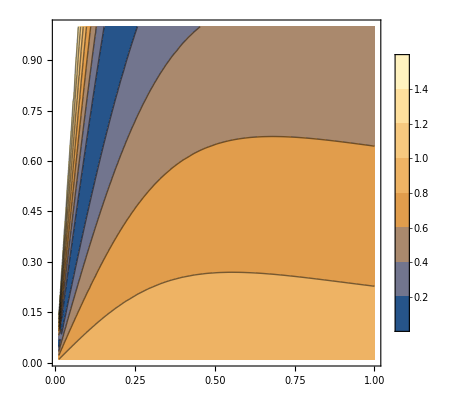

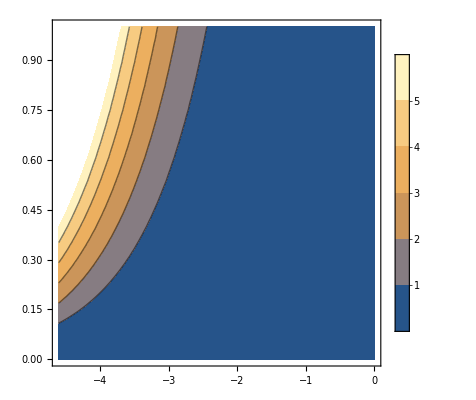

```mathematica
testR3[xbj,ξ,2]//ContourPlot[#,{xbj,0.01,1},{ξ,0.01,1},PlotLegends->Automatic]&
testR3v2[Exp[η], r,2]//ContourPlot[#,{η,Log[0.01],Log[1]},{r,0.0,1},PlotLegends->Automatic]&
```

```mathematica
replacefunctions
```

{zN→(Q^4 zh-M^2 Q^2 xN^2 zh+√(-4 M^2 MB^2 xN^2 (Q^4+M^2 qT^2 xN^2)+(Q^4 zh-M^2 Q^2 xN^2 zh)^2))/(2 (Q^4+M^2 qT^2 xN^2)),xN→(2 xbj)/(1+√(1+(4 M^2 xbj^2)/Q^2)),xNhat→xN/ξ,zNhat→zN/ζ,δkT|kf|kiTbreit→Δk,ki^2→-Δk^2,M→0.9383}

## replacements for plots

```mathematica
(*plots*)
replacefunctions={zN->ZN[zh,xN,qT,MB,M,Q],xN->XN[xbj,M,Q],xNhat->xN/ξ,zNhat->zN/ζ,δkT|kf|kiTbreit->Δk,ki^2->-Δk^2,M->0.9383};
replacekin1={zh->0.25,ξ->0.2,ζ->0.3};
(*replacekin2={zh->0.25,ξ->0.2,ζ->0.40};
replacekin3={zh->0.25,ξ->0.2,ζ->0.70};*)
(*replacekin4={zh->0.25,ξ->0.01,ζ->0.3};
*)
```

## functions for plots

```mathematica
R1function[Q_,xbj_,qT_,MB_,Δk_]=R1//.replacefunctions/.replacekin1;
(*R1functionv3[Q_,xbj_,qT_,MB_,Δk_]=R1//.replacefunctions/.replacekin3;*)

R2function[Q_,xbj_,qT_,MB_,Δk_]=R2//.replacefunctions/.replacekin1;
(*R2functionv2[Q_,xbj_,qT_,MB_,Δk_]=R2//.replacefunctions/.replacekin2;*)
(*R2functionv4[Q_,xbj_,qT_,MB_,Δk_]=R2//.replacefunctions/.replacekin4;*)

R3function[Q_,xbj_,qT_,MB_,Δk_]=R3//.replacefunctions/.replacekin1;


R3functiontest[Q_,xbj_,qT_,MB_,Δk_]=R3test//.{xN->(2 xbj)/(1+√(1+(4 M^2 xbj^2)/Q^2)),xNhat->xN/ξ,δkT|kf|kiTbreit->Δk,ki^2->-Δk^2,M->0.9383}/.replacekin1;
```

Plot style

## legends and labels

```mathematica
legend[title_]:=Placed[BarLegend[Automatic,LegendMarkerSize->281,LegendLabel->Style[title,12,Bold,FontFamily->"Helvetica"],LegendMargins->{{26, 0}, {0, 0}}],Top]

legendv2[title_,range_,contours_,color_,size_,margins_]:=BarLegend[{color,range},contours,LegendMarkerSize->size,LegendLabel->Placed[Style[title,12,FontFamily->"Helvetica"],Top],LegendMargins->margins,LabelStyle->Directive[Black,10,FontFamily->"Helvetica"]]


legendv3[title_,range_,color_,size_,margins_]:=BarLegend[{color,range},LegendMarkerSize->size,LegendLabel->Placed[Style[title,12,Bold,FontFamily->"Helvetica"],Right],LegendMargins->margins,LabelStyle->Directive[Black,10,FontFamily->"Helvetica"]]

labelfunction[id_,vars_,vals_,units_]:=Module[
{label=id<>"   ",table,it,format},
table=Table[(StringForm[(vars[[i]])<>"=`` ``  ",(vals[[i]]//ToString ),(units[[i]]//ToString )])//ToString,{i,1,vars//Length}];
For[it=1,it≤(vals//Length),it++,label=label <>table[[it]]];

format={"xbj"->"x_Bj","zh"->"z_h","qT"->"q_T","MB"->"M_B"};
label= 
label//StringReplace[#,format]&//Style[#,FontFamily->"Helvetica",10]&
]
```

## Plotter, layout and colors

```mathematica
PAD={{40,8},{40,10}};
IMAGESIZE={3.5*72,3.5*72};
COLOR=ColorData["DeepSeaColors"];

color1=Function[{x},ColorData["HypsometricTints"][12000 x - 6000]];
color2=Function[{x},ColorData["BlackBodySpectrum"][9000 x + 1000]];
color3=Function[{x},ColorData["VisibleSpectrum"][370 x + 380]];
color4=Function[{x},Hue[x/2,0.35,0.85,0.94]];
```

```mathematica
plotterR1[function_,label_]:=Module[{functionplot},
ContourPlot[function,{xbj,RANGE[[1,1]],RANGE[[1,2]]},{Q,RANGE[[2,1]],RANGE[[2,2]]},
ColorFunction->COLOR,
ColorFunctionScaling->False,
PlotRange->RANGE,
Contours->CONTOURS,
FrameLabel->{Style[Subscript[x, Bj],10],Style[Q["GeV"],10]},
PlotLabel->label,
LabelStyle->{Black,10,"Helvetica"},
ImagePadding->PAD,ImageMargins->0,
ImageSize->IMAGESIZE]
]

plotterR2[function_,label_]:=Module[{functionplot},
ContourPlot[function,{qT,RANGE[[1,1]],RANGE[[1,2]]},{Q,RANGE[[2,1]],RANGE[[2,2]]},
ColorFunction->COLOR,
ColorFunctionScaling->False,
PlotRange->RANGE,
Contours->CONTOURS,
FrameLabel->{Style[Subscript[q, T]["GeV"],10],Style[Q["GeV"],10]},
PlotLabel->label,
LabelStyle->{Black,10,"Helvetica"},
ImagePadding->PAD,ImageMargins->0,
ImageSize->IMAGESIZE]
]

plotterR3[function_,label_]:=Module[{functionplot},
ContourPlot[function,{qT,RANGE[[1,1]],RANGE[[1,2]]},{Q,RANGE[[2,1]],RANGE[[2,2]]},
ColorFunction->COLOR,
ColorFunctionScaling->False,
PlotRange->RANGE,
Contours->CONTOURS,
FrameLabel->{Style[Subscript[q, T]["GeV"],10],Style[Q["GeV"],10]},
PlotLabel->label,
LabelStyle->{Black,10,"Helvetica"},
ImagePadding->PAD,ImageMargins->0,
ImageSize->IMAGESIZE]
]

plotterR3v2[function_,label_]:=Module[{functionplot},
ContourPlot[function,{xbj,RANGE[[1,1]],RANGE[[1,2]]},{Q,RANGE[[2,1]],RANGE[[2,2]]},
ColorFunction->COLOR,
ColorFunctionScaling->False,
PlotRange->RANGE,
Contours->CONTOURS,
FrameLabel->{Style[Subscript[x, Bj],10],Style[Q["GeV"],10]},
PlotLabel->label,
LabelStyle->{Black,10,"Helvetica"},
ImagePadding->PAD,ImageMargins->0,
ImageSize->IMAGESIZE,
ScalingFunctions->{"Log","Log"}
]
]
```

# Plots for paper

```mathematica
Mdot[kXbreit,kXbreit]/Q^2/.Dot->Times//Expand
```

-1+kf^2/Q^2+ki^2/Q^2+1/xNhat-(ki^2 xNhat)/Q^2-(kiTbreit^2 xNhat)/Q^2-kf^2/(Q^2 zNhat)-(kf^2 ki^2 xNhat)/(Q^4 zNhat)-(kf^2 kiTbreit^2 xNhat)/(Q^4 zNhat)+zNhat-(2 kiTbreit qT zNhat)/Q^2-(qT^2 zNhat)/Q^2-zNhat/xNhat-(ki^2 qT^2 xNhat zNhat)/Q^4-(kiTbreit^2 qT^2 xNhat zNhat)/Q^4+(2 kiTbreit δkT)/Q^2+(2 qT δkT)/Q^2+(2 ki^2 qT xNhat δkT)/Q^4+(2 kiTbreit^2 qT xNhat δkT)/Q^4-δkT^2/(Q^2 zNhat)-(ki^2 xNhat δkT^2)/(Q^4 zNhat)-(kiTbreit^2 xNhat δkT^2)/(Q^4 zNhat)

R1

```mathematica
RANGE={{0.1,0.2},{0.8,2.0},{0,1.0}};
CONTOURS=9;
COLOR=ColorData["CherryTones"][Rescale[#,{0,1},{0.05,0.95}]]&;
(*COLOR=ColorData["CherryTones"][Rescale[#,{0,1},{0.95,0.05}]]&;(*reverse*)
*)
labelR1a=labelfunction["(a)",{"MB","qT"},{0.14,0.3},{"GeV","GeV"}];
labelR1b=labelfunction["(b)",{"MB","qT"},{0.14,2.0},{"GeV","GeV"}];
labelR1c=labelfunction["(c)",{"MB","qT"},{0.50,0.3},{"GeV","GeV"}];
labelR1d=labelfunction["(d)",{"MB","qT"},{0.50,2.0},{"GeV","GeV"}];

legendR1pions=legendv2["R_1(pion)",RANGE[[3]],CONTOURS,COLOR,IMAGESIZE*0.78,{{0,0},{6,0}}];

legendR1kaons=legendv2["R_1(kaon)",RANGE[[3]],CONTOURS,COLOR,IMAGESIZE*0.78,{{0,0},{6,0}}];

plotR1a=plotterR1[R1function[Q,xbj,0.3,0.14,0.3],labelR1a];
plotR1b=plotterR1[R1function[Q,xbj,2.0,0.14,0.3],labelR1b];
plotR1c=plotterR1[R1function[Q,xbj,0.3,0.50,0.3],labelR1c];
plotR1d=plotterR1[R1function[Q,xbj,2.0,0.50,0.3],labelR1d];
```

R2

```mathematica
RANGE={{0.0,2.0},{0.8,2.0},{0,1.0}};
CONTOURS=9;
COLOR=Hue[Rescale[#,RANGE[[3]],{0.05,0.17}],Rescale[#,RANGE[[3]],{1,0.3}],Rescale[#,RANGE[[3]],{0.7,1.}]]&;
(*COLOR=Hue[Rescale[#,{0,1.},{0.17,0.05}],Rescale[#,{0,1},{0.3,1}],Rescale[#,{0,1},{1,0.7}]]&;(*reverse*)
*)

labelR2a=labelfunction["(a)",{"MB","xbj"},{0.14,0.20},{"GeV",""}];
labelR2b=labelfunction["(b)",{"MB","xbj"},{0.14,0.01},{"GeV",""}];
labelR2c=labelfunction["(c)",{"MB","xbj"},{0.50,0.20},{"GeV",""}];
labelR2d=labelfunction["(d)",{"MB","xbj"},{0.50,0.01},{"GeV",""}];

legendR2pions=legendv2["R_2(pion)",RANGE[[3]],CONTOURS,COLOR,IMAGESIZE*0.78,{{0,0},{6,0}}];

legendR2kaons=legendv2["R_2(kaon)",RANGE[[3]],CONTOURS,COLOR,IMAGESIZE*0.78,{{0,0},{6,0}}];

plotR2a=plotterR2[R2function[Q,0.20,qT,0.14,0.3],labelR2a];
plotR2b=plotterR2[R2function[Q,0.01,qT,0.14,0.3],labelR2b];
plotR2c=plotterR2[R2function[Q,0.20,qT,0.50,0.3],labelR2c];
plotR2d=plotterR2[R2function[Q,0.01,qT,0.50,0.3],labelR2d];
```

R3 Q vs qT

```mathematica
RANGE={{0.0,2.0},{0.8,2.0},{0,5.0}};
CONTOURS=9;
COLOR=Hue[Rescale[#,RANGE[[3]],{0.05,0.17}],Rescale[#,RANGE[[3]],{1,0.3}],Rescale[#,RANGE[[3]],{0.7,1.}]]&;
(*COLOR=Hue[Rescale[#,{0,1.},{0.17,0.05}],Rescale[#,{0,1},{0.3,1}],Rescale[#,{0,1},{1,0.7}]]&;(*reverse*)
*)

labelR3a=labelfunction["(a)",{"MB","xbj"},{0.14,0.20},{"GeV",""}];
labelR3b=labelfunction["(b)",{"MB","xbj"},{0.14,0.01},{"GeV",""}];
labelR3c=labelfunction["(c)",{"MB","xbj"},{0.50,0.20},{"GeV",""}];
labelR3d=labelfunction["(d)",{"MB","xbj"},{0.50,0.01},{"GeV",""}];

legendR3pions=legendv2["R_3(pion)",RANGE[[3]],CONTOURS,COLOR,IMAGESIZE*0.78,{{0,0},{6,0}}];

legendR3kaons=legendv2["R_3(kaon)",RANGE[[3]],CONTOURS,COLOR,IMAGESIZE*0.78,{{0,0},{6,0}}];

plotR3a=plotterR3[R3function[Q,0.20,qT,0.14,0.3],labelR3a];
plotR3b=plotterR3[R3function[Q,0.01,qT,0.14,0.3],labelR3b];
plotR3c=plotterR3[R3function[Q,0.20,qT,0.50,0.3],labelR3c];
plotR3d=plotterR3[R3function[Q,0.01,qT,0.50,0.3],labelR3d];
```

```mathematica
?Log
```

Log[z] gives the natural logarithm of z (logarithm to base e). 
Log[b,z] gives the logarithm to base b.

R3 Q vs xbj

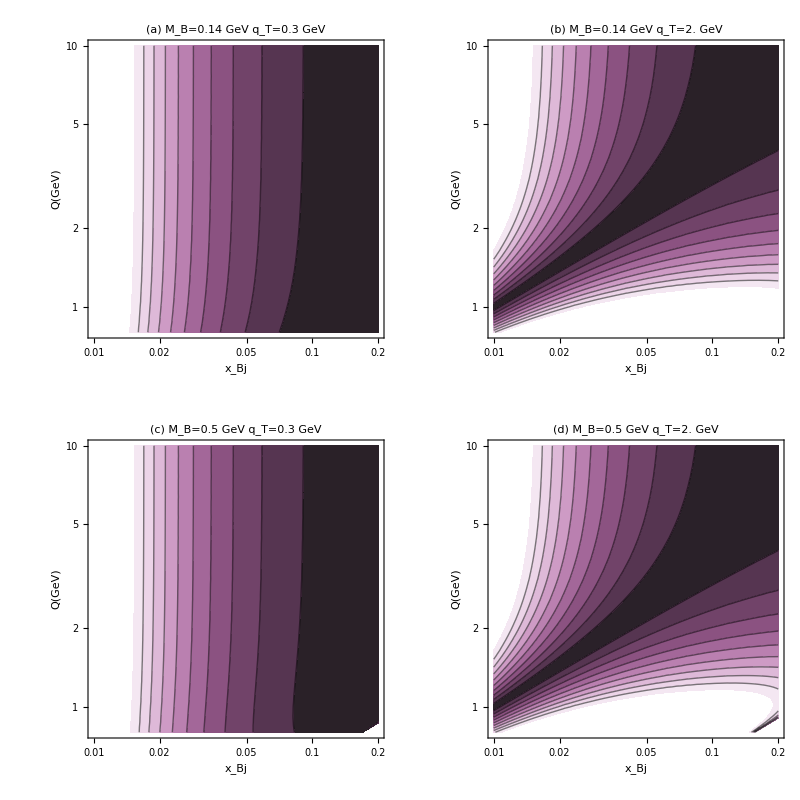

```mathematica
RANGE={{Log[10,0.01],Log[10,1.0]},{0.8,10.0},{0,5.0}};
RANGE={{0.01,0.2},{0.8,10.0},{0,2.0}};
CONTOURS=9;
COLOR=ColorData["FuchsiaTones"][Rescale[#,RANGE[[3]],{0.05,0.95}]]&;
(*COLOR=ColorData["CherryTones"][Rescale[#,{0,1},{0.95,0.05}]]&;(*reverse*)
*)
labelR3av2=labelfunction["(a)",{"MB","qT"},{0.14,0.3},{"GeV","GeV"}];
labelR3bv2=labelfunction["(b)",{"MB","qT"},{0.14,2.0},{"GeV","GeV"}];
labelR3cv2=labelfunction["(c)",{"MB","qT"},{0.50,0.3},{"GeV","GeV"}];
labelR3dv2=labelfunction["(d)",{"MB","qT"},{0.50,2.0},{"GeV","GeV"}];

legendR3pionsv2=legendv2["R_3(pion)",RANGE[[3]],CONTOURS,COLOR,IMAGESIZE*0.78,{{0,0},{6,0}}];

legendR3kaonsv2=legendv2["R_3(kaon)",RANGE[[3]],CONTOURS,COLOR,IMAGESIZE*0.78,{{0,0},{6,0}}];

(*plotR3av2=plotterR3v2[R3function[Q,Power[10,xbj],0.3,0.14,0.3],labelR3av2];
plotR3bv2=plotterR3v2[R3function[Q,Power[10,xbj],2.0,0.14,0.3],labelR3bv2];
plotR3cv2=plotterR3v2[R3function[Q,Power[10,xbj],0.3,0.50,0.3],labelR3cv2];
plotR3dv2=plotterR3v2[R3function[Q,Power[10,xbj],2.0,0.50,0.3],labelR3dv2];*)

plotR3av2=plotterR3v2[R3function[Q,xbj,0.3,0.14,0.3],labelR3av2];
plotR3bv2=plotterR3v2[R3function[Q,xbj,2.0,0.14,0.3],labelR3bv2];
plotR3cv2=plotterR3v2[R3function[Q,xbj,0.3,0.50,0.3],labelR3cv2];
plotR3dv2=plotterR3v2[R3function[Q,xbj,2.0,0.50,0.3],labelR3dv2];

FIGR3v2=GraphicsGrid[
{
{plotR3av2,plotR3bv2,legendR3pionsv2},
{plotR3cv2,plotR3dv2,legendR3kaonsv2}
},
ImageSize-> { IMAGESIZE  2.5,2.IMAGESIZE },
Spacings->0,
Alignment->{{Right,Center,Left}},
ImageMargins->{{0,0},{0,0}},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}
]
```

```mathematica
Export["FIGR3_jogh.pdf",FIGR3v2]
```

FIGR3_jogh.pdf

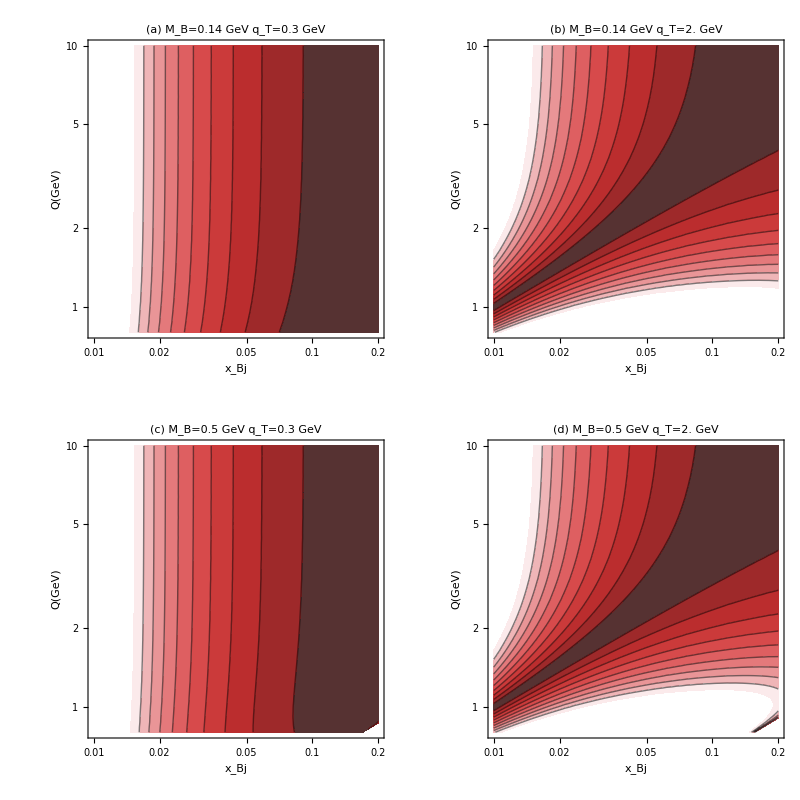

```mathematica
(*FIGR1=GraphicsGrid[
{
{plotR1a,plotR1b,legendR1pions},
{plotR1c,plotR1d,legendR1kaons}
},
ImageSize-> { IMAGESIZE  2.5,2.IMAGESIZE },
Spacings->0,
Alignment->{{Right,Center,Left}},
ImageMargins->{{0,0},{0,0}},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}
]
FIGR2=GraphicsGrid[
{
{plotR2a,plotR2b,legendR2pions},
{plotR2c,plotR2d,legendR2kaons}
},
ImageSize-> { IMAGESIZE  2.5,2.IMAGESIZE },
Spacings->0,
Alignment->{{Right,Center,Left}},
ImageMargins->{{0,0},{0,0}},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}
]

FIGR3=GraphicsGrid[
{
{plotR3a,plotR3b,legendR3pions},
{plotR3c,plotR3d,legendR3kaons}
},
ImageSize-> { IMAGESIZE  2.5,2.IMAGESIZE },
Spacings->0,
Alignment->{{Right,Center,Left}},
ImageMargins->{{0,0},{0,0}},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}
]*)
FIGR3v2=GraphicsGrid[
{
{plotR3av2,plotR3bv2,legendR3pionsv2},
{plotR3cv2,plotR3dv2,legendR3kaonsv2}
},
ImageSize-> { IMAGESIZE  2.5,2.IMAGESIZE },
Spacings->0,
Alignment->{{Right,Center,Left}},
ImageMargins->{{0,0},{0,0}},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}
]
```

```mathematica
ColorData["Gradients"][[22]]
```

FuchsiaTones

```mathematica
replacekin1
```

{zh→0.25,ξ→0.2,ζ→0.3}

```mathematica
Log[0.01]
Log[0.3]
```

-4.60517

-1.20397

R3

```mathematica
R3functiontest[1,0.1,0.3,0.14,0.3]
R3function[1,0.1,0.3,0.14,0.3]
```

0.088576

0.0989705

```mathematica
replacefunctions
```

0.126838

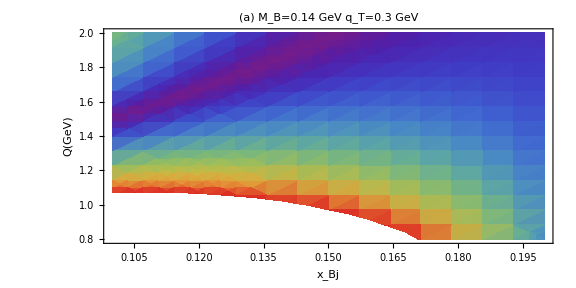

```mathematica
replacetemp={zN->(Q^4 zh-M^2 Q^2 xN^2 zh+√(-4 M^2 MB^2 xN^2 (Q^4+M^2 qT^2 xN^2)+(Q^4 zh-M^2 Q^2 xN^2 zh)^2))/(2 (Q^4+M^2 qT^2 xN^2)),xN->(2 xbj)/(1+√(1+(4 M^2 xbj^2)/Q^2)),xNhat->xN/ξ,zNhat->zN/ζ,δkT->Δk,kf|kiTbreit->0,ki^2->0,M->0.93};
replacetemp={zN->(Q^4 zh-M^2 Q^2 xN^2 zh+√(-4 M^2 MB^2 xN^2 (Q^4+M^2 qT^2 xN^2)+(Q^4 zh-M^2 Q^2 xN^2 zh)^2))/(2 (Q^4+M^2 qT^2 xN^2)),xN->(2 xbj)/(1+√(1+(4 M^2 xbj^2)/Q^2)),xNhat->xN/ξ,zNhat->zN/ζ,ki^2->-Δk^2,kf |δkT|kiTbreit->0,ki^2->0,M->0.93};
R3functiontest[Q_,xbj_,qT_,MB_,Δk_]=R3test2//.replacetemp/.replacekin1;
R3functiontest[1,0.1,0.2,0.14,0.2]


RANGE={{0.1,0.2},{0.8,2.0},{0.0,0.15}};
(*plotR3v2a=plotterR3v2[R3function[Q,xbj,0.3,0.14,0.5],labelR3v2a];
plotR3v2a*)
ASPECT=1/2;
plotR3v2atest=plotterR3v2[R3functiontest[Q,xbj,0.3,0.14,0.8]^2//Sqrt,labelR3v2a];
Show[plotR3v2atest,ImageSize->Large]
```

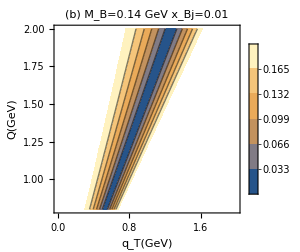

-Graphics-

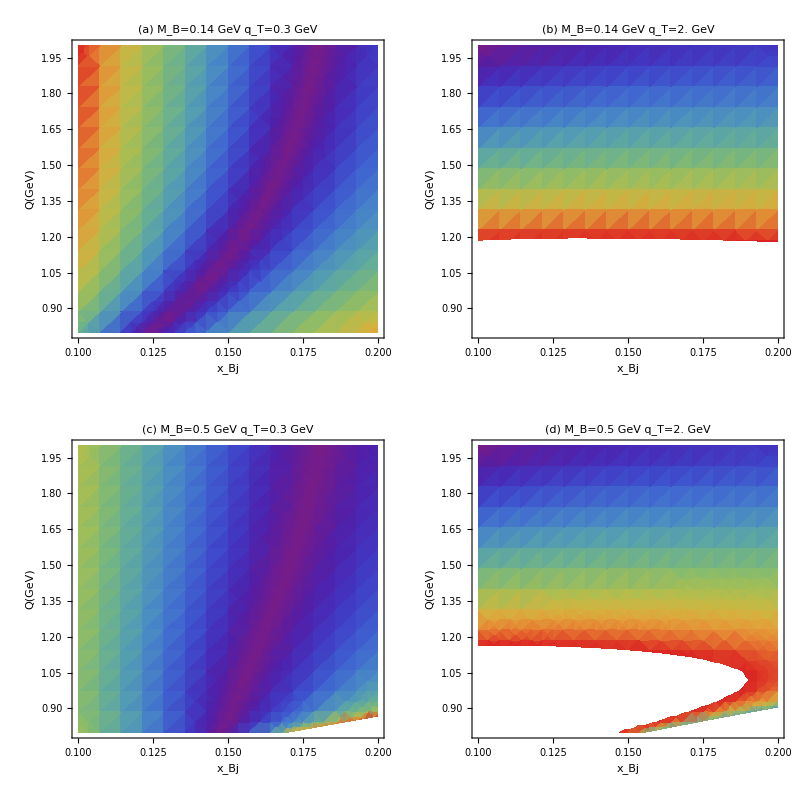

```mathematica
RANGE={{0.0,2.0},{0.8,2.0},{0.0,0.2}};
CONTOURS=5;
COLOR=Hue[Rescale[#,RANGE[[3]],{0.05,0.17}],Rescale[#,RANGE[[3]],{1,0.3}],Rescale[#,RANGE[[3]],{0.7,1.}]]&;
(*COLOR=Hue[Rescale[#,{0,1.},{0.17,0.05}],Rescale[#,{0,1},{0.3,1}],Rescale[#,{0,1},{1,0.7}]]&;(*reverse*)
*)

labelR3a=labelfunction["(a)",{"MB","xbj"},{0.14,0.20},{"GeV",""}];
labelR3b=labelfunction["(b)",{"MB","xbj"},{0.14,0.01},{"GeV",""}];
labelR3c=labelfunction["(c)",{"MB","xbj"},{0.50,0.20},{"GeV",""}];
labelR3d=labelfunction["(d)",{"MB","xbj"},{0.50,0.01},{"GeV",""}];

legendR3pions=legendv2["R_3(pion)",RANGE[[3]],CONTOURS,COLOR,IMAGESIZE*0.78,{{0,0},{6,0}}];

legendR3kaons=legendv2["R_3(kaon)",RANGE[[3]],CONTOURS,COLOR,IMAGESIZE*0.78,{{0,0},{6,0}}];

plotR3a=plotterR3[R3function[Q,0.20,qT,0.14,0.3],labelR3a];
plotR3b=plotterR3[R3function[Q,0.07,qT,0.14,0.3],labelR3b]
plotR3c=plotterR3[R3function[Q,0.20,qT,0.50,0.3],labelR3c];
plotR3d=plotterR3[R3function[Q,0.07,qT,0.50,0.3],labelR3d];

RANGE={{0.1,0.2},{0.8,2.0},{-2,2.0}};
CONTOURS=9;
COLOR=ColorData["CherryTones"][Rescale[#,{0,1},{0.05,0.95}]]&;
(*COLOR=ColorData["CherryTones"][Rescale[#,{0,1},{0.95,0.05}]]&;(*reverse*)
*)
labelR3v2a=labelfunction["(a)",{"MB","qT"},{0.14,0.3},{"GeV","GeV"}];
labelR3v2b=labelfunction["(b)",{"MB","qT"},{0.14,2.0},{"GeV","GeV"}];
labelR3v2c=labelfunction["(c)",{"MB","qT"},{0.50,0.3},{"GeV","GeV"}];
labelR3v2d=labelfunction["(d)",{"MB","qT"},{0.50,2.0},{"GeV","GeV"}];

legendR3v2pions=legendv2["R_3(pion)",RANGE[[3]],CONTOURS,COLOR,IMAGESIZE*0.78,{{0,0},{6,0}}];

legendR3v2kaons=legendv2["R_3(kaon)",RANGE[[3]],CONTOURS,COLOR,IMAGESIZE*0.78,{{0,0},{6,0}}];

plotR3v2a=plotterR3v2[R3function[Q,xbj,0.3,0.14,0.3],labelR3v2a];
plotR3v2b=plotterR3v2[R3function[Q,xbj,2.0,0.14,0.3],labelR3v2b];
plotR3v2c=plotterR3v2[R3function[Q,xbj,0.3,0.50,0.3],labelR3v2c];
plotR3v2d=plotterR3v2[R3function[Q,xbj,2.0,0.50,0.3],labelR3v2d];

FIGR3=GraphicsGrid[
{
{plotR3a,plotR3b,legendR3pions},
{plotR3c,plotR3d,legendR3kaons}
},
ImageSize-> { IMAGESIZE  2.5,2.IMAGESIZE },
Spacings->0,
Alignment->{{Right,Center,Left}},
ImageMargins->{{0,0},{0,0}},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}
]
FIGR3v2=GraphicsGrid[
{
{plotR3v2a,plotR3v2b,legendR3v2pions},
{plotR3v2c,plotR3v2d,legendR3v2kaons}
},
ImageSize-> { IMAGESIZE  2.5,2.IMAGESIZE },
Spacings->0,
Alignment->{{Right,Center,Left}},
ImageMargins->{{0,0},{0,0}},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}
]
```

```mathematica
replacekin1
```

{zh→0.25,ξ→0.2,ζ→0.3}

Global`R3function

R3function[Q_,xbj_,qT_,MB_,Δk_]=√(1/Q^4((-(2.77778 qT^2 (0.25 Q^4-(0.880407 Q^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2)+√((0.25 Q^4-(0.880407 Q^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2))^2-(14.0865 MB^2 xbj^2 (Q^4+(3.52163 qT^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2)))/((1+√(1+(3.52163 xbj^2)/Q^2))^2)))^2)/((Q^4+(3.52163 qT^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2))^2)+(0.06 (1+√(1+(3.52163 xbj^2)/Q^2)) (Q^4+(3.52163 qT^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2)) (-1+(1.66667 (0.25 Q^4-(0.880407 Q^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2)+√((0.25 Q^4-(0.880407 Q^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2))^2-(14.0865 MB^2 xbj^2 (Q^4+(3.52163 qT^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2)))/((1+√(1+(3.52163 xbj^2)/Q^2))^2))))/(Q^4+(3.52163 qT^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2))) ((1.66667 Q^2 (-1+(10. xbj)/(1+√(1+(3.52163 xbj^2)/Q^2))) (0.25 Q^4-(0.880407 Q^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2)+√((0.25 Q^4-(0.880407 Q^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2))^2-(14.0865 MB^2 xbj^2 (Q^4+(3.52163 qT^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2)))/((1+√(1+(3.52163 xbj^2)/Q^2))^2))))/(Q^4+(3.52163 qT^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2))+(10. xbj Δk^2)/(1+√(1+(3.52163 xbj^2)/Q^2))+1/(1+√(1+(3.52163 xbj^2)/Q^2))10. xbj ((2.77778 qT^2 (0.25 Q^4-(0.880407 Q^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2)+√((0.25 Q^4-(0.880407 Q^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2))^2-(14.0865 MB^2 xbj^2 (Q^4+(3.52163 qT^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2)))/((1+√(1+(3.52163 xbj^2)/Q^2))^2)))^2)/((Q^4+(3.52163 qT^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2))^2)-(3.33333 qT (0.25 Q^4-(0.880407 Q^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2)+√((0.25 Q^4-(0.880407 Q^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2))^2-(14.0865 MB^2 xbj^2 (Q^4+(3.52163 qT^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2)))/((1+√(1+(3.52163 xbj^2)/Q^2))^2))) Δk)/(Q^4+(3.52163 qT^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2))+Δk^2)))/(xbj (0.25 Q^4-(0.880407 Q^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2)+√((0.25 Q^4-(0.880407 Q^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2))^2-(14.0865 MB^2 xbj^2 (Q^4+(3.52163 qT^2 xbj^2)/((1+√(1+(3.52163 xbj^2)/Q^2))^2)))/((1+√(1+(3.52163 xbj^2)/Q^2))^2))))))^2)

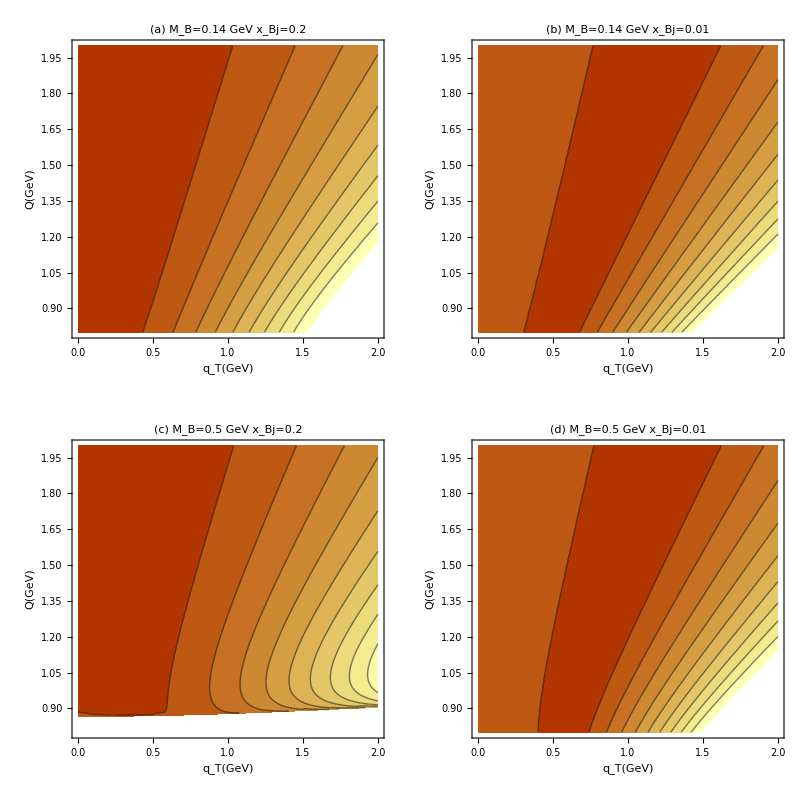

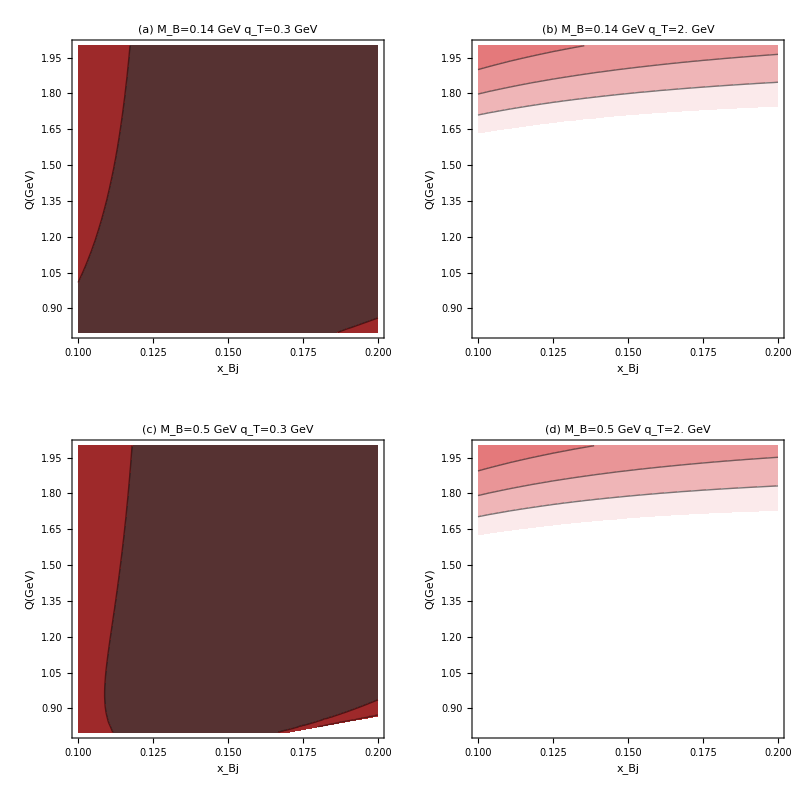

```mathematica
?R3function
```

```mathematica
kinematicstest={Q->1.5,xbj->0.1,zh->0.25,MB->0.14,Δk->0.3,M->0.9383,ξ->0.2,ζ->0.3};
replacefunctionstest={zN->(Q^4 zh-M^2 Q^2 xN^2 zh+√(-4 M^2 MB^2 xN^2 (Q^4+M^2 qT^2 xN^2)+(Q^4 zh-M^2 Q^2 xN^2 zh)^2))/(2 (Q^4+M^2 qT^2 xN^2)),xN->(2 xbj)/(1+√(1+(4 M^2 xbj^2)/Q^2)),xNhat->xN/ξ,zNhat->zN/ζ,δkT|kf|kiTbreit->Δk,ki^2->-Δk^2};
```

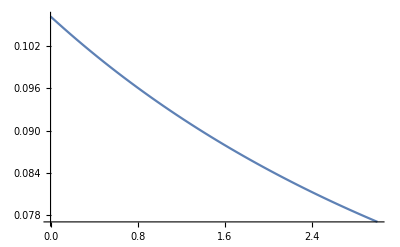

```mathematica
test[qT_]=R1//.replacefunctions/.kinematicstest;
Plot[test[qT],{qT,0,3}]
```

```mathematica
W2SIDIS=Pbreit+qbreit-PBbreit//Mdot[#,#]&//ReplaceRepeated[#,{zN->(ZN//getfunction//Apart//FullSimplify),xN->(XN//getfunction//Apart//FullSimplify)}]&//Apart//Simplify;
```

(a)   q_T=0 GeV  z_h=0.25

(b)   q_T=2. GeV  z_h=0.25

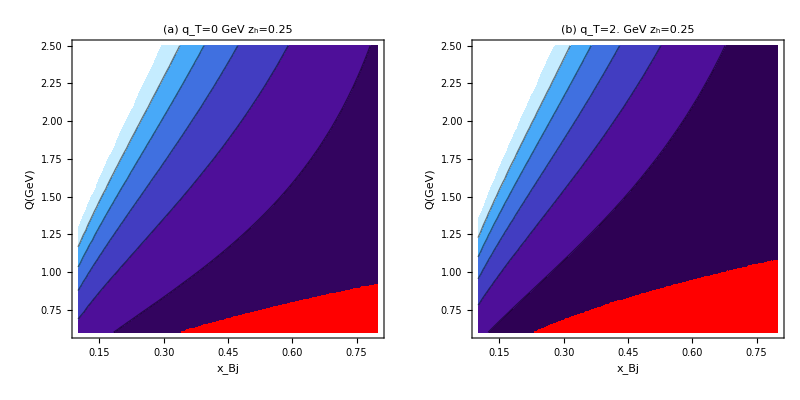

FIGW2sidis_jogh.pdf

```mathematica
plotW2SIDIS[kin_,label_]:=Module[
{region1,region2,functionplot,functionplotraw,plotallowed,plotnotallowed,color,colorfixed},

functionplot[xbj_,Q_]=(W2SIDIS//.kin);
color=ColorData["DeepSeaColors"][Rescale[#,RANGE[[3]],{0,1.}]]&;
colorfixed=RGBColor[Rescale[#,{-∞,∞},{1,1}],0,0]&;
plotallowed=ContourPlot[functionplot[xbj,Q],{xbj,RANGE[[1,1]],RANGE[[1,2]]},{Q,RANGE[[2,1]],RANGE[[2,2]]},
ColorFunction->color,
PlotRange->RANGE,
ColorFunctionScaling->False,
Contours->CONTOURS,
FrameLabel->{Style[Subscript[x, Bj],10],Style[Q["GeV"],10]},
PlotLabel->label,
LabelStyle->{Black,10,"Helvetica"},
ImagePadding->PAD,
ImageMargins->0,
ImageSize->IMAGESIZE,
LabelStyle->{10,"Helvetica",Black},
RegionFunction->(Im[#3]==0&)

];

plotnotallowed=ContourPlot[(functionplot[xbj,Q]//Im),{xbj,RANGE[[1,1]],RANGE[[1,2]]},{Q,RANGE[[2,1]],RANGE[[2,2]]},
ColorFunction->colorfixed,
PlotRange->{RANGE[[1]],RANGE[[2]],Full},
ColorFunctionScaling->False,
ImagePadding->PAD,
ImageMargins->0,
ImageSize->IMAGESIZE,
ContourStyle->None,
Contours->{0.001},
RegionFunction->(#3>0&)

];
Show[plotallowed,plotnotallowed]
]

(*pad={{40,10},{40,10}};
IMAGESIZE={3.5*72,3.5*72};*)
RANGE={{0.1,0.8},{0.6,2.5},{0,12}};
CONTOURS=5;
COLOR=ColorData["DeepSeaColors"][Rescale[#,RANGE[[3]],{0,1}]]&;
kinW2SIDIS1={zh->0.25,qT->0,MB->0.14,M->0.9383};
kinW2SIDIS2={zh->0.25,qT->2.0,MB->0.14,M->0.9383};

legendv4[title_,range_,contours_,color_,size_,margins_]:=BarLegend[{color,range},contours,LegendMarkerSize->size,LegendLabel->Placed[Style[title,10,FontFamily->"Helvetica"],Top],LegendMargins->margins,LabelStyle->Directive[Black,10,FontFamily->"Helvetica"]]


legendW2sidis=legendv4["W_SIDIS^2",RANGE[[3]],CONTOURS,COLOR,IMAGESIZE*0.78,{{0,0},{6,0}}];

labelW2SIDIS1=labelfunction["(a)",{"qT","zh"},{qT,zh}/.kinW2SIDIS1,{"GeV",""}]
plotW2SIDIS1=plotW2SIDIS[kinW2SIDIS1,labelW2SIDIS1];

labelW2SIDIS2=labelfunction["(b)",{"qT","zh"},{qT,zh}/.kinW2SIDIS2,{"GeV",""}]
plotW2SIDIS2=plotW2SIDIS[kinW2SIDIS2,labelW2SIDIS2];

FIGW2sidis=GraphicsGrid[
{
{plotW2SIDIS1,plotW2SIDIS2,legendW2sidis}
},
ImageSize-> { IMAGESIZE  2.5,IMAGESIZE },
Spacings->0,
Alignment->{{Right,Center,Left}},
ImageMargins->{{0,0},{0,0}},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}
]
Export["FIGW2sidis_jogh.pdf",FIGW2sidis]
```

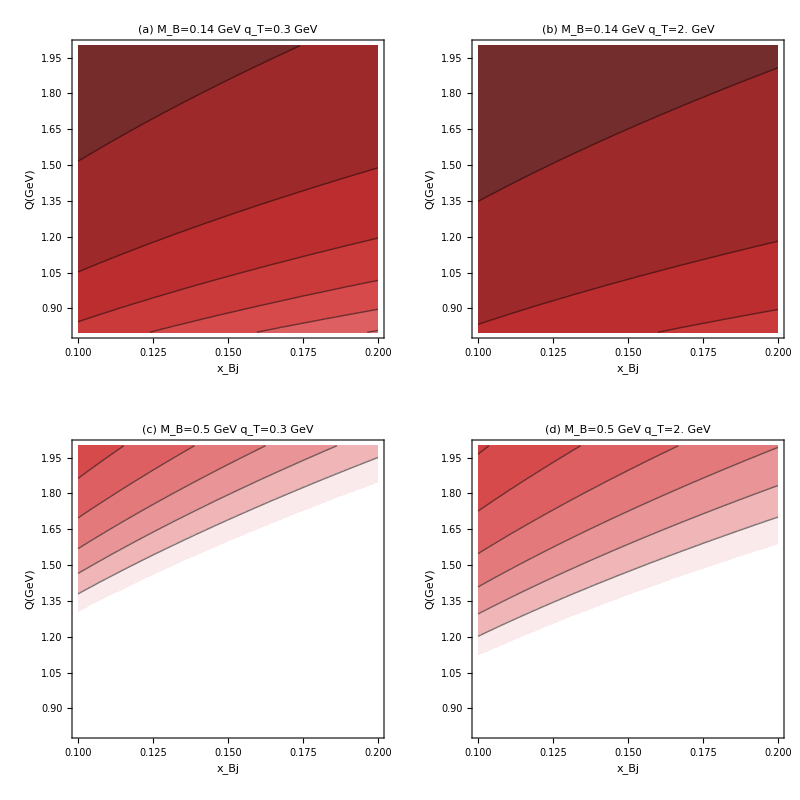
{-Graphics-,-Graphics-}

```mathematica
{FIGR1,FIGW2sidis}
```